# Thesis Plots

## Intialisation

```mathematica
setChapDir[name_]:=SetDirectory[FileNameJoin[{NotebookDirectory[],"Figures",name,"PlotData"}]]
Needs["ErrorBarPlots`"]
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16,FontColor->Black},ImageSize->600,Frame->True,Axes->False];
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[Histogram,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[DateListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[ErrorListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
```

myGridDivision can be used to set some kind of style for major and minor grids

```mathematica
myGridDivision[{min_,max_},{major_,majorStyle_},{minor_,minorStyle_}]:=Function[divisions,Join[{#,majorStyle}&/@divisions[[1]],{#,minorStyle}&/@Complement[Flatten[#[[2]]],#[[1]]]&@divisions]][FindDivisions[{min,max},{major,minor}]]
Colours=Darker[#]&/@{Red,Green,Blue,Black,Purple,Yellow,Brown,Orange,Pink,Gray,Cyan,Magenta};
```

```mathematica
plotExport[plot_,name_]:=Export["../"<>name<>".pdf",plot]
```

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.
Export[file,expr,elems,relems] returns to the Wolfram System the elements specified by relems.

## Chapter 1

## Chapter 2

## Chapter 3

This section focuses on the experimental setup

```mathematica
setChapDir["Chapter3"]
```

/media/Storage/Dropbox/PhDWork/Thesis/Figures/Chapter3/PlotData

## Muquans Spectra

### Sat. Spec Signal

```mathematica
satspec = Import["satspec.csv"];
```

The 3,4 Rb85 crossover is at 384.2291813694837 THz. All frequencies will be shifted relative to that, in units of MHz

```mathematica
satdata={(#⟦1⟧-384.2291813694837)*10^6,#⟦2⟧+1.18}&/@satspec;
```

```mathematica
satspecPlot=ListPlot[satdata,GridLines->{myGridDivision[{-1500,1000},{5,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}],myGridDivision[{-2,4},{10,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}]},FrameStyle->Thick,FrameLabel->{"Detuning from^85Rb F=3 → F'=3,4 crossover (MHz)","abs. signal (arb. units)"}]
```

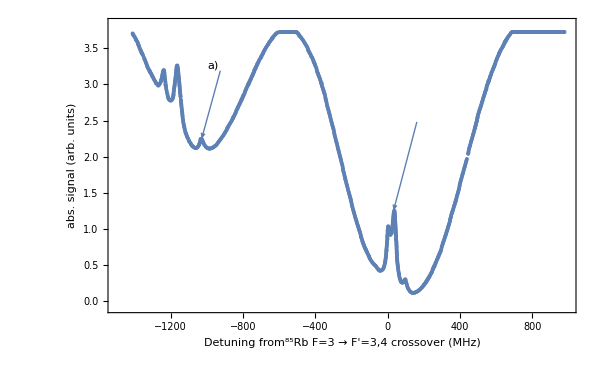

```mathematica
plotExport[satspecPlot,"sat_spec"]
```

### Error Signal

### Slave 0 Error

### Slave 1 Error